## Calculation of an example singular value plot (Ch. 3)

```mathematica
G0 =TransferFunctionModel[ ({{1/(1+ s), 1/(1+ τ s)}, {1/(1+  τ s), 1/(1+  s)}}),s] /. τ -> 1/2
```

1/(1+s)1/(1+s/2)1/(1+s/2)1/(1+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s22111111111FalseFalseFalseAutomaticNoneAutomatic

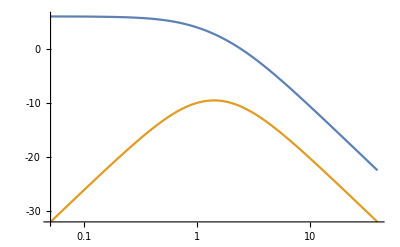

```mathematica
svp =SingularValuePlot[G0]
```